## PDH and other laser locking

## Pound-Drever-Hall (PDH) locking

Mark’s optics notes 13.4.1

## Dither locking

```mathematica
laser[t_] :=1/(1+t^2); 
mod[α_,t_]:=α Cos[2π 100 t];
```

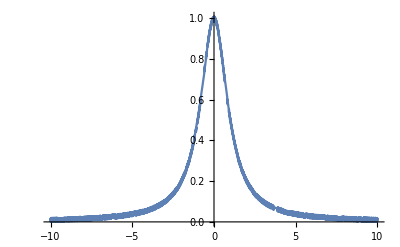

```mathematica
Plot[mod[.01,t]+laser[t],{t,-10,10},PlotRange->All]
```